```mathematica
Cases[{f[1],g[2],f[2],f[5],g[3], f[3]},f[1|5]]
```

{f[1],f[5]}

```mathematica
Cases[{1,2.5,3.5,4},_Real]
Cases[{1,2.5,3.5,4},_Integer]
```

{2.5,3.5}

{1,4}

```mathematica
f[#] &/@{1,2.5,3.5,4}
```

{f[1],f[2.5],f[3.5],f[4]}

```mathematica
Cases[{f[1],f[2.5],f[3.5],f[4]}, f[_Real]]
```

{f[2.5],f[3.5]}

```mathematica
Cases[{f[1],f[2.5],f[3.5],f[4]}, f[_Integer]]
```

{f[1],f[4]}

```mathematica
x=4;x=.;x+2
```

2+x

```mathematica
{a,b,c,d,e,f}[[2;;-3]]
```

{b,c,d}

```mathematica
Table[i/j,{i,4},{j,2}]
```

{{1,1/2},{2,1},{3,3/2},{4,2}}

```mathematica
Table[i/j,{i,4}]
```

{1/j,2/j,3/j,4/j}

```mathematica
Table[x^2,{x,0,4}]
```

{0,1,4,9,16}

```mathematica
a = 3
Module[{a=1},a+8]
a
```

3

9

3

```mathematica
{f[1],g[2],f[5],g[3]}/. f[x_]-> x^2
```

{1,g[2],25,g[3]}

```mathematica
Cases[{f[1,2],f[1],g[3], f[1,2,3]},f[__]]
```

{f[1,2],f[1],f[1,2,3]}

```mathematica
Cases[{f[1,2],f[1],g[3], f[1,2,3]},f[_, _]]
```

{f[1,2]}

```mathematica
ClearAll[f, x]
f[1]=2
f[x_] := x^2 /; x ∈ Reals
{f[1],f[2],f[3],f[4], f[Pi]}


ClearAll[f, x]
f[1]=2
notIntegerQ := (!IntegerQ[#]) &
f[x_notIntegerQ] := x^2 
{f[1],f[2],f[3]f[4], f[Pi] // FullForm}
```

2

{2,4,9,16,π^2}

2

{2,f[2],f[3] f[4],f[Pi]}

```mathematica
f =.
f[u[x_]]:=x+1
f[v[x_]]:=x-1
f[u[1]]
f[v[1]]
```

2

0

```mathematica
x =.

Solve[((x+1)/x)^2 - ((x+1)/(x-1))^2 == 1, x]
```

{{x→-√(-2+√5)},{x→√(-2+√5)},{x→-ⅈ √(2+√5)},{x→ⅈ √(2+√5)}}

```mathematica
FullSimplify[√(-2+√5)]
```

√(-2+√5)

```mathematica
ClearAll[f,a,b,c,d]
Map[f,{{a,b},{c,d}}]
Map[f,{{a,b},{c,d}}, {1}]
Map[f,{{a,b},{c,d}}, {2}]
Map[f,{{a,b},{c,d}}, {3}]
Map[f,{{a,b},{c,d}}, {4}]
```

{f[{a,b}],f[{c,d}]}

{f[{a,b}],f[{c,d}]}

{{f[a],f[b]},{f[c],f[d]}}

{{a,b},{c,d}}

{{a,b},{c,d}}

```mathematica
Apply[f,{a,b,c,d}]
```

f[a,b,c,d]

```mathematica
f@{{a,b},{c,d}}
f@@{{a,b},{c,d}}
f@@@{{a,b},{c,d}}
f@{x,y}
f@@{x,y}
f@@@{x,y}
```

f[{{a,b},{c,d}}]

f[{a,b},{c,d}]

{f[a,b],f[c,d]}

f[{x,y}]

f[x,y]

{x,y}

```mathematica
Apply[f,{{a,b},{c,d}}, 0]
Apply[f,{{a,b},{c,d}}, 1]
Apply[f,{a,b,c,d}, 2]
Apply[f,{a,b,c,d}, {2}]
Apply[f,{a,b,c,d}, {1}]
```

{{a,b},{c,d}}

{f[a,b],f[c,d]}

{a,b,c,d}

{a,b,c,d}

{a,b,c,d}

```mathematica
Select[#>7&][{1,4,6,8,10,15}]
Select[{1,4,6,8,10,15},#>7&]
```

{8,10,15}

{8,10,15}

```mathematica
n = Nearest[{1,4,6,8,10,15}]
```

NearestFunction[…]

```mathematica
n[5]
n[5.5]
```

{4,6}

{6}

```mathematica
Options[Framed] // Column
```

Alignment→Automatic
Background→None
BaselinePosition→Automatic
BaseStyle→{}
ContentPadding→True
DefaultBaseStyle→{}
DefaultFrameStyle→{}
FrameMargins→Automatic
FrameStyle→Automatic
ImageMargins→0
ImageSize→Automatic
RoundingRadius→0
StripOnInput→False

```mathematica
TabView[{a -> 4,b -> 2,c -> 3}]
```

123

```mathematica
Button["do it",Speak["hello"]]
```

do it

```mathematica
Slider[Dynamic[x]]
```

```mathematica
Dynamic[x]
```

```mathematica
Manipulate[ListLinePlot[{1,3,x,4,1,3,x}],{x,1,4}]
```

```mathematica
a=0;Module[{a=1},a+1]
```

2

```mathematica
x=2;y=5;Print[x+y]//FullForm
x=2;y=5;FullForm[x + y]
```

7

Null

7

```mathematica
ClearAll[h,x,y]
x = 3
h = <|"a"->Dynamic[x],"b"->{y,3}|>
```

3

<|a→,b→{y,3}|>

```mathematica
Dynamic[h["a"]]
```

```mathematica
x = 5
```

5

```mathematica
{#b, #b^2}& [h]
h[["b", 1]]
h[["b", 2]]
```

{{y,3},{y^2,9}}

y

3

```mathematica
TemplateApply["first `a`; second `b`; first `a`",<|"a"->x,"b"->y|>]
```

first 3; second y; first 3

```mathematica
ClearAll[x,y, m]
m = <|"a"->x,"b"->y|>
m["a"]
m["b"]
m["c"] -> 3
{#a, #b^2}& [m]
```

<|a→x,b→y|>

x

y

Missing[KeyAbsent,c]→3

{x,y^2}

```mathematica
<|"a"->x,"b"->{5,6}|>[["b",1]]
```

5

```mathematica
TemplateApply["first `a`; second `b`; first `a`",<|"a"->x,"b"->y|>]
```

first x; second y; first x

```mathematica
m=<|"a"->x,"b"->y|>;
AssociateTo[m,<|"c"->z|>];
m
```

<|a→x,b→y,c→z|>

WolframAlphaQueryResults

WolframAlphaQueryNoResults

WolframAlphaQueryResults

(data not available) | (based on 0 values; 8 unavailable)

WolframAlphaQueryParseResults

-Graphics-

WolframAlphaQueryNoResults

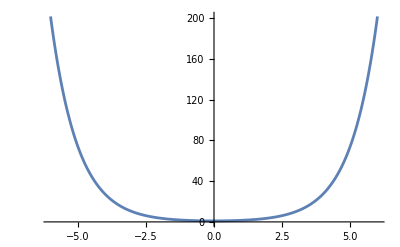

```mathematica
Plot[Evaluate[Cosh[x]], {x, -6., 6.}]
```

picture of the computer graphics Utah teapot

WolframAlphaQueryResults

```mathematica
ed = EarthquakeData[Entity["Country","UnitedStates"], {4, 10}, PreviousDate["Year"]]
```

<|ncnc73827571→<|Period→Sun 1 Jan 2023 14:35:05GMT-4,AzimuthalGap→44 °,Depth→30.63 km,Identifier→ncnc73827571,Magnitude→5.35,MagnitudeType→mw,NumberOfPhases→56,NumberOfStations→37,Position→GeoPosition[{40.409,-123.971}],PositionMethod→Null|>,ncnc73834441→<|Period→Fri 20 Jan 2023 04:01:15GMT-4,AzimuthalGap→89 °,Depth→25.27 km,Identifier→ncnc73834441,Magnitude→4.26,MagnitudeType→mw,NumberOfPhases→84,NumberOfStations→80,Position→GeoPosition[{41.128,-123.875}],PositionMethod→Null|>,usus6000jke7→<|Period→Mon 30 Jan 2023 15:28:52GMT-4,AzimuthalGap→100 °,Depth→5. km,Identifier→usus6000jke7,Magnitude→4.1,MagnitudeType→ml,NumberOfPhases→24,NumberOfStations→21,Position→GeoPosition[{45.7468,-110.586}],PositionMethod→Null|>,txtx2023dgvx→<|Period→Thu 16 Feb 2023 06:29:05GMT-4,AzimuthalGap→70 °,Depth→8.65698 km,Identifier→txtx2023dgvx,Magnitude→4.7,MagnitudeType→ml,NumberOfPhases→41,NumberOfStations→26,Position→GeoPosition[{32.7448,-100.652}],PositionMethod→Null|>,usus6000jpbv→<|Period→Thu 16 Feb 2023 06:29:06GMT-4,AzimuthalGap→22 °,Depth→1.799 km,Identifier→usus6000jpbv,Magnitude→4.3,MagnitudeType→mwr,NumberOfPhases→128,NumberOfStations→118,Position→GeoPosition[{32.7518,-100.637}],PositionMethod→Null|>,txtx2023drpm→<|Period→Wed 22 Feb 2023 03:44:10GMT-4,AzimuthalGap→45 °,Depth→6.64573 km,Identifier→txtx2023drpm,Magnitude→4.2,MagnitudeType→ml,NumberOfPhases→63,NumberOfStations→50,Position→GeoPosition[{31.6735,-104.375}],PositionMethod→Null|>,txus6000jqqu→<|Period→Wed 22 Feb 2023 03:44:10GMT-4,AzimuthalGap→73 °,Depth→6.13157 km,Identifier→txus6000jqqu,Magnitude→4.1,MagnitudeType→ml,NumberOfPhases→35,NumberOfStations→21,Position→GeoPosition[{31.6726,-104.374}],PositionMethod→Null|>,txtx2023drrr→<|Period→Wed 22 Feb 2023 04:51:25GMT-4,AzimuthalGap→46 °,Depth→7.2113 km,Identifier→txtx2023drrr,Magnitude→4.,MagnitudeType→ml,NumberOfPhases→61,NumberOfStations→45,Position→GeoPosition[{31.6722,-104.368}],PositionMethod→Null|>,txus6000jqr9→<|Period→Wed 22 Feb 2023 04:51:25GMT-4,AzimuthalGap→46 °,Depth→7.2113 km,Identifier→txus6000jqr9,Magnitude→4.,MagnitudeType→ml,NumberOfPhases→61,NumberOfStations→45,Position→GeoPosition[{31.6722,-104.368}],PositionMethod→Null|>,txtx2023edto→<|Period→Tue 28 Feb 2023 19:26:09GMT-4,AzimuthalGap→50 °,Depth→8.48385 km,Identifier→txtx2023edto,Magnitude→4.1,MagnitudeType→ml,NumberOfPhases→62,NumberOfStations→45,Position→GeoPosition[{31.6135,-103.989}],PositionMethod→Null|>,usus_7000jgd3_mwr→<|Period→Tue 28 Feb 2023 19:26:09GMT-4,AzimuthalGap→53 °,Depth→8.829 km,Identifier→usus_7000jgd3_mwr,Magnitude→4.,MagnitudeType→mwr,NumberOfPhases→46,NumberOfStations→41,Position→GeoPosition[{31.6119,-103.978}],PositionMethod→Null|>,usus_7000jiqv_mwr→<|Period→Fri 10 Mar 2023 02:06:47GMT-4,AzimuthalGap→66 °,Depth→1.841 km,Identifier→usus_7000jiqv_mwr,Magnitude→4.3,MagnitudeType→mwr,NumberOfPhases→43,NumberOfStations→39,Position→GeoPosition[{37.1976,-104.698}],PositionMethod→Null|>,usus7000jiqv→<|Period→Fri 10 Mar 2023 02:06:48GMT-4,AzimuthalGap→58 °,Depth→6.275 km,Identifier→usus7000jiqv,Magnitude→4.3,MagnitudeType→mwr,NumberOfPhases→56,NumberOfStations→52,Position→GeoPosition[{37.1872,-104.734}],PositionMethod→Null|>,usus_7000jiyi_mwr→<|Period→Fri 10 Mar 2023 16:31:36GMT-4,AzimuthalGap→70 °,Depth→5. km,Identifier→usus_7000jiyi_mwr,Magnitude→4.3,MagnitudeType→ml,NumberOfPhases→20,NumberOfStations→15,Position→GeoPosition[{37.1638,-104.722}],PositionMethod→Null|>,cici39508378→<|Period→Fri 31 Mar 2023 21:16:08GMT-4,AzimuthalGap→18 °,Depth→12.96 km,Identifier→cici39508378,Magnitude→4.15,MagnitudeType→mw,NumberOfPhases→295,NumberOfStations→153,Position→GeoPosition[{33.3817,-116.91}],PositionMethod→Null|>,ncnc73866925→<|Period→Tue 4 Apr 2023 18:23:18GMT-4,AzimuthalGap→48 °,Depth→10.16 km,Identifier→ncnc73866925,Magnitude→4.41,MagnitudeType→mw,NumberOfPhases→126,NumberOfStations→111,Position→GeoPosition[{36.801,-121.323}],PositionMethod→Null|>,okogs2023gsgn→<|Period→Thu 6 Apr 2023 04:57:17GMT-4,AzimuthalGap→32 °,Depth→7. km,Identifier→okogs2023gsgn,Magnitude→4.,MagnitudeType→mwr,NumberOfPhases→181,NumberOfStations→99,Position→GeoPosition[{35.7935,-96.9698}],PositionMethod→Null|>,usus6000k2b9→<|Period→Thu 6 Apr 2023 04:57:17GMT-4,AzimuthalGap→31 °,Depth→6. km,Identifier→usus6000k2b9,Magnitude→4.,MagnitudeType→mwr,NumberOfPhases→77,NumberOfStations→55,Position→GeoPosition[{35.791,-96.9669}],PositionMethod→Null|>,ncnc73871215→<|Period→Wed 12 Apr 2023 01:39:52GMT-4,AzimuthalGap→24 °,Depth→2.45 km,Identifier→ncnc73871215,Magnitude→4.43,MagnitudeType→mw,NumberOfPhases→114,NumberOfStations→103,Position→GeoPosition[{38.8352,-122.807}],PositionMethod→Null|>,cici40214151→<|Period→Sat 29 Apr 2023 08:07:04GMT-4,AzimuthalGap→43 °,Depth→10.43 km,Identifier→cici40214151,Magnitude→4.1,MagnitudeType→mw,NumberOfPhases→94,NumberOfStations→57,Position→GeoPosition[{32.711,-115.545}],PositionMethod→Null|>,cici40215575→<|Period→Sun 30 Apr 2023 03:09:34GMT-4,AzimuthalGap→88 °,Depth→2.04 km,Identifier→cici40215575,Magnitude→4.33,MagnitudeType→mw,NumberOfPhases→100,NumberOfStations→65,Position→GeoPosition[{33.2008,-115.59}],PositionMethod→Null|>,cici40215583→<|Period→Sun 30 Apr 2023 03:10:10GMT-4,AzimuthalGap→87 °,Depth→1.88 km,Identifier→cici40215583,Magnitude→4.29,MagnitudeType→mw,NumberOfPhases→96,NumberOfStations→55,Position→GeoPosition[{33.1893,-115.593}],PositionMethod→Null|>,cici40215735→<|Period→Sun 30 Apr 2023 03:58:19GMT-4,AzimuthalGap→90 °,Depth→1.89 km,Identifier→cici40215735,Magnitude→4.26,MagnitudeType→mw,NumberOfPhases→111,NumberOfStations→68,Position→GeoPosition[{33.2037,-115.586}],PositionMethod→Null|>,ncnc73886731-1683871759848→<|Period→Thu 11 May 2023 19:19:42GMT-4,AzimuthalGap→46 °,Depth→5.85 km,Identifier→ncnc73886731-1683871759848,Magnitude→5.48,MagnitudeType→mw,NumberOfPhases→56,NumberOfStations→54,Position→GeoPosition[{40.2042,-121.109}],PositionMethod→Null|>,ncnc73887046→<|Period→Fri 12 May 2023 06:18:41GMT-4,AzimuthalGap→37 °,Depth→6.06 km,Identifier→ncnc73887046,Magnitude→5.16,MagnitudeType→mw,NumberOfPhases→51,NumberOfStations→49,Position→GeoPosition[{40.196,-121.1}],PositionMethod→Null|>,cici40230055→<|Period→Sat 20 May 2023 23:26:30GMT-4,AzimuthalGap→163 °,Depth→5.29 km,Identifier→cici40230055,Magnitude→4.26,MagnitudeType→mw,NumberOfPhases→29,NumberOfStations→18,Position→GeoPosition[{37.2837,-117.584}],PositionMethod→Null|>,ncnc73890170→<|Period→Fri 26 May 2023 07:26:25GMT-4,AzimuthalGap→46 °,Depth→6.71 km,Identifier→ncnc73890170,Magnitude→4.13,MagnitudeType→mw,NumberOfPhases→43,NumberOfStations→41,Position→GeoPosition[{40.2267,-121.148}],PositionMethod→Null|>,ncnc73895826→<|Period→Sat 3 Jun 2023 08:01:19GMT-4,AzimuthalGap→25 °,Depth→3.83 km,Identifier→ncnc73895826,Magnitude→4.45,MagnitudeType→mw,NumberOfPhases→107,NumberOfStations→106,Position→GeoPosition[{38.7922,-122.779}],PositionMethod→Null|>,ncnc73902356→<|Period→Sat 17 Jun 2023 23:44:59GMT-4,AzimuthalGap→64 °,Depth→10.52 km,Identifier→ncnc73902356,Magnitude→4.35,MagnitudeType→mw,NumberOfPhases→101,NumberOfStations→92,Position→GeoPosition[{39.0893,-123.09}],PositionMethod→Null|>,usus7000k9kq→<|Period→Mon 19 Jun 2023 10:18:56GMT-4,AzimuthalGap→39 °,Depth→4.887 km,Identifier→usus7000k9kq,Magnitude→4.3,MagnitudeType→mb,NumberOfPhases→71,NumberOfStations→56,Position→GeoPosition[{37.3017,-104.447}],PositionMethod→Null|>,usus7000kfv7→<|Period→Fri 14 Jul 2023 18:26:09GMT-4,AzimuthalGap→26 °,Depth→11.621 km,Identifier→usus7000kfv7,Magnitude→4.2,MagnitudeType→mwr,NumberOfPhases→81,NumberOfStations→67,Position→GeoPosition[{44.6097,-112.598}],PositionMethod→Null|>,nnnn00862704→<|Period→Sun 16 Jul 2023 00:36:10GMT-4,AzimuthalGap→39 °,Depth→8. km,Identifier→nnnn00862704,Magnitude→4.,MagnitudeType→ml,NumberOfPhases→31,NumberOfStations→20,Position→GeoPosition[{38.5412,-118.162}],PositionMethod→Null|>,nnus7000kg2h→<|Period→Sun 16 Jul 2023 00:36:10GMT-4,AzimuthalGap→39 °,Depth→8. km,Identifier→nnus7000kg2h,Magnitude→4.,MagnitudeType→ml,NumberOfPhases→31,NumberOfStations→20,Position→GeoPosition[{38.5412,-118.162}],PositionMethod→Null|>,nnus_7000kgsq_mwr→<|Period→Wed 19 Jul 2023 03:34:22GMT-4,AzimuthalGap→67 °,Depth→2.1 km,Identifier→nnus_7000kgsq_mwr,Magnitude→4.9,MagnitudeType→ml,NumberOfPhases→45,NumberOfStations→45,Position→GeoPosition[{39.5157,-116.563}],PositionMethod→Null|>,nnnn00862970→<|Period→Wed 19 Jul 2023 03:34:24GMT-4,AzimuthalGap→46 °,Depth→3.7 km,Identifier→nnnn00862970,Magnitude→4.5,MagnitudeType→mw,NumberOfPhases→12,NumberOfStations→8,Position→GeoPosition[{39.5107,-116.536}],PositionMethod→Null|>,cici39627442→<|Period→Wed 2 Aug 2023 01:38:09GMT-4,AzimuthalGap→89 °,Depth→3.11 km,Identifier→cici39627442,Magnitude→4.12,MagnitudeType→mw,NumberOfPhases→104,NumberOfStations→67,Position→GeoPosition[{33.186,-115.574}],PositionMethod→Null|>,ncnc73922596→<|Period→Thu 10 Aug 2023 15:17:18GMT-4,AzimuthalGap→54 °,Depth→9.5 km,Identifier→ncnc73922596,Magnitude→4.28,MagnitudeType→mw,NumberOfPhases→86,NumberOfStations→72,Position→GeoPosition[{35.9345,-120.484}],PositionMethod→Null|>,ncnc73925281→<|Period→Thu 17 Aug 2023 17:08:01GMT-4,AzimuthalGap→49 °,Depth→31.93 km,Identifier→ncnc73925281,Magnitude→4.07,MagnitudeType→mw,NumberOfPhases→60,NumberOfStations→42,Position→GeoPosition[{40.3183,-124.234}],PositionMethod→Null|>,cici39645386→<|Period→Sun 20 Aug 2023 17:41:01GMT-4,AzimuthalGap→27 °,Depth→4.84 km,Identifier→cici39645386,Magnitude→5.08,MagnitudeType→mw,NumberOfPhases→175,NumberOfStations→115,Position→GeoPosition[{34.4085,-119.188}],PositionMethod→Null|>,txtx2023qlls→<|Period→Tue 22 Aug 2023 18:58:00GMT-4,AzimuthalGap→68 °,Depth→7.93113 km,Identifier→txtx2023qlls,Magnitude→4.,MagnitudeType→ml,NumberOfPhases→50,NumberOfStations→40,Position→GeoPosition[{31.6606,-104.316}],PositionMethod→Null|>,usus7000kq7r→<|Period→Tue 22 Aug 2023 18:58:00GMT-4,AzimuthalGap→65 °,Depth→5. km,Identifier→usus7000kq7r,Magnitude→4.,MagnitudeType→mb,NumberOfPhases→39,NumberOfStations→34,Position→GeoPosition[{31.6382,-104.298}],PositionMethod→Null|>,usus7000kr5e→<|Period→Sat 26 Aug 2023 04:38:45GMT-4,AzimuthalGap→42 °,Depth→4.158 km,Identifier→usus7000kr5e,Magnitude→4.,MagnitudeType→mwr,NumberOfPhases→58,NumberOfStations→52,Position→GeoPosition[{36.9895,-104.926}],PositionMethod→Null|>,usus_7000kr5e_mwr→<|Period→Sat 26 Aug 2023 04:38:45GMT-4,AzimuthalGap→42 °,Depth→4.158 km,Identifier→usus_7000kr5e_mwr,Magnitude→4.,MagnitudeType→mwr,NumberOfPhases→58,NumberOfStations→52,Position→GeoPosition[{36.9895,-104.926}],PositionMethod→Null|>,ncnc73934641→<|Period→Fri 8 Sep 2023 13:24:38GMT-4,AzimuthalGap→33 °,Depth→15.63 km,Identifier→ncnc73934641,Magnitude→4.99,MagnitudeType→mw,NumberOfPhases→46,NumberOfStations→41,Position→GeoPosition[{40.953,-121.56}],PositionMethod→Null|>,ncnc71131324→<|Period→Fri 8 Sep 2023 13:25:06GMT-4,AzimuthalGap→90 °,Depth→12.44 km,Identifier→ncnc71131324,Magnitude→4.33,MagnitudeType→ml,NumberOfPhases→19,NumberOfStations→15,Position→GeoPosition[{40.9618,-121.571}],PositionMethod→Null|>,txtx2023sbec→<|Period→Thu 14 Sep 2023 14:50:42GMT-4,AzimuthalGap→50 °,Depth→5.42896 km,Identifier→txtx2023sbec,Magnitude→4.,MagnitudeType→ml,NumberOfPhases→27,NumberOfStations→27,Position→GeoPosition[{29.0753,-97.8647}],PositionMethod→Null|>,usus7000kvtk→<|Period→Thu 14 Sep 2023 14:50:42GMT-4,AzimuthalGap→114 °,Depth→10.703 km,Identifier→usus7000kvtk,Magnitude→4.,MagnitudeType→mb,NumberOfPhases→33,NumberOfStations→32,Position→GeoPosition[{29.0673,-97.8242}],PositionMethod→Null|>,ncnc73938736→<|Period→Tue 19 Sep 2023 00:13:10GMT-4,AzimuthalGap→91 °,Depth→3.51 km,Identifier→ncnc73938736,Magnitude→4.53,MagnitudeType→mw,NumberOfPhases→180,NumberOfStations→174,Position→GeoPosition[{37.4382,-121.296}],PositionMethod→Null|>,ncnc73943821→<|Period→Sat 30 Sep 2023 11:26:27GMT-4,AzimuthalGap→166 °,Depth→17.88 km,Identifier→ncnc73943821,Magnitude→4.65,MagnitudeType→mw,NumberOfPhases→64,NumberOfStations→45,Position→GeoPosition[{40.5588,-124.289}],PositionMethod→Null|>,ncnc73944166→<|Period→Sun 1 Oct 2023 11:41:30GMT-4,AzimuthalGap→105 °,Depth→9.8 km,Identifier→ncnc73944166,Magnitude→4.09,MagnitudeType→mw,NumberOfPhases→59,NumberOfStations→42,Position→GeoPosition[{40.2952,-124.287}],PositionMethod→Null|>,txtx2023tumb→<|Period→Mon 9 Oct 2023 09:59:25GMT-4,AzimuthalGap→92 °,Depth→3.9861 km,Identifier→txtx2023tumb,Magnitude→4.,MagnitudeType→ml(tex,NumberOfPhases→33,NumberOfStations→30,Position→GeoPosition[{28.966,-97.62}],PositionMethod→Null|>,txus_6000le8z_mwr→<|Period→Mon 9 Oct 2023 09:59:25GMT-4,AzimuthalGap→95 °,Depth→7.5321 km,Identifier→txus_6000le8z_mwr,Magnitude→4.1,MagnitudeType→ml(tex,NumberOfPhases→43,NumberOfStations→28,Position→GeoPosition[{28.956,-97.623}],PositionMethod→Null|>,ncnc73947830→<|Period→Mon 16 Oct 2023 06:20:50GMT-4,AzimuthalGap→52 °,Depth→31.06 km,Identifier→ncnc73947830,Magnitude→4.83,MagnitudeType→mw,NumberOfPhases→56,NumberOfStations→45,Position→GeoPosition[{40.3157,-124.055}],PositionMethod→Null|>,ncnc73948665→<|Period→Wed 18 Oct 2023 12:29:15GMT-4,AzimuthalGap→20 °,Depth→8.46 km,Identifier→ncnc73948665,Magnitude→4.24,MagnitudeType→mw,NumberOfPhases→157,NumberOfStations→157,Position→GeoPosition[{38.127,-121.643}],PositionMethod→Null|>,ncnc73952605→<|Period→Sat 28 Oct 2023 01:40:19GMT-4,AzimuthalGap→112 °,Depth→4.46 km,Identifier→ncnc73952605,Magnitude→4.24,MagnitudeType→mw,NumberOfPhases→28,NumberOfStations→23,Position→GeoPosition[{38.5572,-119.51}],PositionMethod→Null|>,cici39706674→<|Period→Fri 3 Nov 2023 16:12:18GMT-4,AzimuthalGap→25 °,Depth→6.91 km,Identifier→cici39706674,Magnitude→4.02,MagnitudeType→mw,NumberOfPhases→154,NumberOfStations→105,Position→GeoPosition[{34.4215,-119.17}],PositionMethod→Null|>,txtx2023vqsh→<|Period→Sat 4 Nov 2023 19:39:56GMT-4,AzimuthalGap→45 °,Depth→6.7251 km,Identifier→txtx2023vqsh,Magnitude→4.1,MagnitudeType→ml(tex,NumberOfPhases→53,NumberOfStations→30,Position→GeoPosition[{32.312,-101.828}],PositionMethod→Null|>,txus7000l8x2→<|Period→Sat 4 Nov 2023 19:39:56GMT-4,AzimuthalGap→63 °,Depth→6.4805 km,Identifier→txus7000l8x2,Magnitude→4.2,MagnitudeType→ml(tex,NumberOfPhases→27,NumberOfStations→14,Position→GeoPosition[{32.312,-101.828}],PositionMethod→Null|>,txtx2023vqus→<|Period→Sat 4 Nov 2023 20:49:52GMT-4,AzimuthalGap→59 °,Depth→6.9941 km,Identifier→txtx2023vqus,Magnitude→4.1,MagnitudeType→ml(tex,NumberOfPhases→43,NumberOfStations→25,Position→GeoPosition[{32.309,-101.827}],PositionMethod→Null|>,txus7000l8xk→<|Period→Sat 4 Nov 2023 20:49:52GMT-4,AzimuthalGap→62 °,Depth→6.7006 km,Identifier→txus7000l8xk,Magnitude→4.,MagnitudeType→ml(tex,NumberOfPhases→31,NumberOfStations→16,Position→GeoPosition[{32.313,-101.827}],PositionMethod→Null|>,txtx2023vxae→<|Period→Wed 8 Nov 2023 06:27:49GMT-4,AzimuthalGap→52 °,Depth→7.417 km,Identifier→txtx2023vxae,Magnitude→5.2,MagnitudeType→ml(tex,NumberOfPhases→39,NumberOfStations→31,Position→GeoPosition[{31.622,-103.982}],PositionMethod→Null|>,usus_7000l9j8_mww→<|Period→Wed 8 Nov 2023 06:27:49GMT-4,AzimuthalGap→53 °,Depth→8.027 km,Identifier→usus_7000l9j8_mww,Magnitude→5.2,MagnitudeType→mww,NumberOfPhases→46,NumberOfStations→43,Position→GeoPosition[{31.6128,-103.971}],PositionMethod→Null|>,nnnn00868733→<|Period→Fri 10 Nov 2023 11:30:44GMT-4,AzimuthalGap→44 °,Depth→12.7 km,Identifier→nnnn00868733,Magnitude→4.3,MagnitudeType→ml,NumberOfPhases→21,NumberOfStations→13,Position→GeoPosition[{38.1859,-117.854}],PositionMethod→Null|>,usus7000la9a→<|Period→Fri 10 Nov 2023 20:18:42GMT-4,AzimuthalGap→37 °,Depth→5. km,Identifier→usus7000la9a,Magnitude→4.,MagnitudeType→mwr,NumberOfPhases→41,NumberOfStations→33,Position→GeoPosition[{39.0471,-97.6158}],PositionMethod→Null|>,txtx2023wzka→<|Period→Thu 23 Nov 2023 19:14:35GMT-4,AzimuthalGap→56 °,Depth→7.6054 km,Identifier→txtx2023wzka,Magnitude→4.2,MagnitudeType→ml(tex,NumberOfPhases→25,NumberOfStations→19,Position→GeoPosition[{32.409,-102.019}],PositionMethod→Null|>,cici39720706→<|Period→Fri 1 Dec 2023 03:43:27GMT-4,AzimuthalGap→29 °,Depth→8.69 km,Identifier→cici39720706,Magnitude→4.8,MagnitudeType→mw,NumberOfPhases→155,NumberOfStations→95,Position→GeoPosition[{32.7518,-115.873}],PositionMethod→Null|>,ciew1701416610→<|Period→Fri 1 Dec 2023 03:43:28GMT-4,AzimuthalGap→29 °,Depth→9.6 km,Identifier→ciew1701416610,Magnitude→4.54,MagnitudeType→mlr,NumberOfPhases→114,NumberOfStations→104,Position→GeoPosition[{32.7495,-115.869}],PositionMethod→Null|>,txtx2023xtoa→<|Period→Mon 4 Dec 2023 19:59:09GMT-4,AzimuthalGap→69 °,Depth→6.5943 km,Identifier→txtx2023xtoa,Magnitude→4.,MagnitudeType→ml,NumberOfPhases→28,NumberOfStations→21,Position→GeoPosition[{31.666,-104.376}],PositionMethod→Null|>,usus_7000lga1_mwr→<|Period→Mon 4 Dec 2023 19:59:09GMT-4,AzimuthalGap→61 °,Depth→7.607 km,Identifier→usus_7000lga1_mwr,Magnitude→4.,MagnitudeType→mwr,NumberOfPhases→44,NumberOfStations→40,Position→GeoPosition[{31.659,-104.365}],PositionMethod→Null|>,usus7000lhz1→<|Period→Sun 10 Dec 2023 15:31:19GMT-4,AzimuthalGap→34 °,Depth→7.053 km,Identifier→usus7000lhz1,Magnitude→4.2,MagnitudeType→mb,NumberOfPhases→34,NumberOfStations→29,Position→GeoPosition[{40.1656,-98.2907}],PositionMethod→Null|>,uwuw61977871→<|Period→Sun 24 Dec 2023 11:14:04GMT-4,AzimuthalGap→20 °,Depth→52.39 km,Identifier→uwuw61977871,Magnitude→4.04,MagnitudeType→ml,NumberOfPhases→222,NumberOfStations→132,Position→GeoPosition[{47.8197,-122.96}],PositionMethod→Null|>|>

earthquakes in the US in the last year

WolframAlphaQueryResults

```mathematica
to = Entity["City",{"Toronto","Ontario","Canada"}]
```

Toronto

```mathematica
Entity["City",{"Toronto","Ontario","Canada"}]
```

Toronto

```mathematica
to//FullForm
EntityValue[to, "Population"]
EntityValue[to, "Mayor"]
```

Entity["City",List["Toronto","Ontario","Canada"]]

2731571 people

Missing[UnknownProperty,{City,Mayor}]

```mathematica
Entity["City",{"LosAngeles","California","UnitedStates"}]
```

Los Angeles

```mathematica
EntityValue[to, "Elevation"]
```

92. m

```mathematica
to["MedianHomeValue"]
```

Missing[NotAvailable]

```mathematica
tov = {#, to[#]}& /@ {"ActiveHomeListingCount","AdministrativeDivision","AggravatedAssault","AggravatedAssaultRate","AggregateHomeValue","AggregateHomeValue15To24","AggregateHomeValue25To34","AggregateHomeValue35To64","AggregateHomeValue65","AggregateHouseholdIncome","AirportCodes","AnnualExcessFuelConsumedPerCommuter","AnnualExcessFuelConsumedTotal","AnnualHoursOfDelayPerAutoCommuter","AnnualHoursOfDelayTotal","Area","AreaCodes","ArterialStreetDailyVehicleMiles","ArterialStreetLaneMiles","AverageHomeListingPrice","AveragePublicTransitTripLength","Burglary","BurglaryRate","CitySalesTaxRate","Coordinates","Country","County","CountySalesTaxRate","CrimeRate","CrimeTotal","DailyDelayMinutes","Elevation","EntityClasses","EntityTypeList","ForcibleRape","ForcibleRapeRate","FreewayDailyVehicle-Miles","FreewayLaneMiles","GiniIndex","HasPolygon","HousePriceIndex","HousePriceIndexAnnualAverage","HousingAffordability","HousingPriceIncreasedCount","HousingPriceReducedCount","HousingUnits","LarcenyTheft","LarcenyTheftRate","Latitude","Longitude","MagneticFieldStrength","MedianAge","MedianDaysOnHousingMarket","MedianHomeListingPrice","MedianHomeListingPricePerSquareFeet","MedianHomeSalePrice","MedianHomeSizeInSquareFeet","MedianHomeValue","MedianHouseholdIncome","MetropolitanArea","MotorVehicleTheft","MotorVehicleTheftRate","MurderNonnegligentManslaughter","MurderNonnegligentManslaughterRate","Name","NewHomeListingCount","NextDSTShift","Nicknames","NumberOfHomes","PeakPeriodTravelers","PeakPeriodTravelersPerCapita","PeakPeriodVehicles","PendingHomeListCount","PeopleBornInCity","PeopleDiedInCity","PerCapitaIncome","Polygon","Population","PopulationByEducationalAttainment","PopulationByGeographicalMobility","PopulationByLanguageSpokenAtHome","PopulationByMaritalStatus","PopulationByPovertyStatus","PopulationBySchoolEnrollment","PopulationDensity","Position","PreviousDSTShift","PropertyCrimeRate","PropertyCrimeTotal","PublicTransportationAnnualPassengerMiles","PublicTransportationAnnualUnlinkedPassengerTrips","RentFourBedrooms","RentOneBedrooms","RentThreeBedrooms","RentTwoBedrooms","RentZeroBedrooms","Robbery","RobberyRate","RushHours","StateSalesTaxRate","TimeZone","TotalDailyDelay","TotalSalesTaxRate","TravelTimeIndex","UnemploymentRate","UnweightedSampleHousingUnits","UnweightedSamplePopulation","ViolentCrimeRate","ViolentCrimeTotal","ZIPCodes"}
```

{{ActiveHomeListingCount,Missing[NotAvailable]},{AdministrativeDivision,Ontario, Canada},{AggravatedAssault,Missing[NotAvailable]},{AggravatedAssaultRate,Missing[NotAvailable]},{AggregateHomeValue,Missing[NotAvailable]},{AggregateHomeValue15To24,Missing[NotAvailable]},{AggregateHomeValue25To34,Missing[NotAvailable]},{AggregateHomeValue35To64,Missing[NotAvailable]},{AggregateHomeValue65,Missing[NotAvailable]},{AggregateHouseholdIncome,Missing[NotAvailable]},{AirportCodes,{Armour Heights Field,Barker Field,Cardinal Couriers Heliport,Buttonville,Toronto City Centre Airport,Toronto Pearson International Airport,Downsview Airport,De Lesseps Field,Leaside Aerodrome,Markham Airport,Markham Stouffville Heliport,Tarten Heliport,Toronto Aerodrome,Toronto (Hospital For Sick Children) Heliport,Toronto (Mississauga Credit Valley Hospital) Heliport,Toronto (St. Michael's Hospital) Heliport,Toronto (Sunnybrook Medical Centre) Heliport,Willowdale Airfield,Wilson's Heliport}},{AnnualExcessFuelConsumedPerCommuter,Missing[NotAvailable]},{AnnualExcessFuelConsumedTotal,Missing[NotAvailable]},{AnnualHoursOfDelayPerAutoCommuter,Missing[NotAvailable]},{AnnualHoursOfDelayTotal,Missing[NotAvailable]},{Area,630.21 km^2},{AreaCodes,Missing[NotAvailable]},{ArterialStreetDailyVehicleMiles,Missing[NotAvailable]},{ArterialStreetLaneMiles,Missing[NotAvailable]},{AverageHomeListingPrice,Missing[NotAvailable]},{AveragePublicTransitTripLength,Missing[NotAvailable]},{Burglary,Missing[NotAvailable]},{BurglaryRate,Missing[NotAvailable]},{CitySalesTaxRate,Missing[NotAvailable]},{Coordinates,{43.65,-79.38}},{Country,Canada},{County,Missing[NotAvailable]},{CountySalesTaxRate,Missing[NotAvailable]},{CrimeRate,Missing[NotAvailable]},{CrimeTotal,Missing[NotAvailable]},{DailyDelayMinutes,Missing[NotAvailable]},{Elevation,92. m},{EntityClasses,{}},{EntityTypeList,{city}},{ForcibleRape,Missing[NotAvailable]},{ForcibleRapeRate,Missing[NotAvailable]},{FreewayDailyVehicle-Miles,Missing[NotAvailable]},{FreewayLaneMiles,Missing[NotAvailable]},{GiniIndex,Missing[NotAvailable]},{HasPolygon,True},{HousePriceIndex,Missing[NotAvailable]},{HousePriceIndexAnnualAverage,Missing[NotAvailable]},{HousingAffordability,Missing[NotAvailable]},{HousingPriceIncreasedCount,Missing[NotAvailable]},{HousingPriceReducedCount,Missing[NotAvailable]},{HousingUnits,Missing[NotAvailable]},{LarcenyTheft,Missing[NotAvailable]},{LarcenyTheftRate,Missing[NotAvailable]},{Latitude,43.65 °},{Longitude,-79.38 °},{MagneticFieldStrength,53.1465 μT},{MedianAge,Missing[NotAvailable]},{MedianDaysOnHousingMarket,Missing[NotAvailable]},{MedianHomeListingPrice,Missing[NotAvailable]},{MedianHomeListingPricePerSquareFeet,Missing[NotAvailable]},{MedianHomeSalePrice,Missing[NotAvailable]},{MedianHomeSizeInSquareFeet,Missing[NotAvailable]},{MedianHomeValue,Missing[NotAvailable]},{MedianHouseholdIncome,Missing[NotAvailable]},{MetropolitanArea,Toronto},{MotorVehicleTheft,Missing[NotAvailable]},{MotorVehicleTheftRate,Missing[NotAvailable]},{MurderNonnegligentManslaughter,Missing[NotAvailable]},{MurderNonnegligentManslaughterRate,Missing[NotAvailable]},{Name,Toronto},{NewHomeListingCount,Missing[NotAvailable]},{NextDSTShift,Missing[NotAvailable]},{Nicknames,{Economic Engine of Canada,Hogtown,Queen City,The Festival City,T.O.,T-Dot,The Big Smoke,Hollywood North,The Most Multicultural City in the World}},{NumberOfHomes,Missing[NotAvailable]},{PeakPeriodTravelers,Missing[NotAvailable]},{PeakPeriodTravelersPerCapita,Missing[NotAvailable]},{PeakPeriodVehicles,Missing[NotAvailable]},{PendingHomeListCount,Missing[NotAvailable]},{PeopleBornInCity,{Daniel Levy→Tue 9 Aug 1983,Drake→Fri 24 Oct 1986,The Weeknd→Fri 16 Feb 1990,Emma Raducanu→Wed 13 Nov 2002,Norman Jewison→Wed 21 Jul 1926,Patrick J. Adams→Thu 27 Aug 1981,Corey Haim→Thu 23 Dec 1971,Catherine O'Hara→Thu 4 Mar 1954,John Candy→Tue 31 Oct 1950,Christopher Plummer→Fri 13 Dec 1929,Will Arnett→Mon 4 May 1970,Dan Markel→Mon 9 Oct 1972,RJ Barrett→Wed 14 Jun 2000,Neil Young→Mon 12 Nov 1945,Robbie Robertson→Mon 5 Jul 1943,Nora Fatehi→Thu 6 Feb 1992,Mae Martin→Sat 2 May 1987,Jesse Palmer→Thu 5 Oct 1978,Mike Myers→Sat 25 May 1963,Rick Moranis→Sat 18 Apr 1953,Tara Strong→Mon 12 Feb 1973,Cory Doctorow→Sat 17 Jul 1971,Sarah Levy→Wed 10 Sep 1986,Katheryn Winnick→Sat 17 Dec 1977,Dave Foley→Fri 4 Jan 1963,Robbie Amell→Thu 21 Apr 1988,Howie Mandel→Tue 29 Nov 1955,Lorne Michaels→Fri 17 Nov 1944,Andrew Wiggins→Thu 23 Feb 1995,David Cronenberg→Mon 15 Mar 1943,Geddy Lee→Wed 29 Jul 1953,Rick Fox→Thu 24 Jul 1969,Sarah Gadon→Sat 4 Apr 1987,Stephen Amell→Fri 8 May 1981,Alison Pill→Wed 27 Nov 1985,Deryck Whibley→Fri 21 Mar 1980,Nancy Dolman→Wed 26 Sep 1951,Chris Diamantopoulos→Fri 9 May 1975,Sarah Polley→Mon 8 Jan 1979,Michael Ironside→Sun 12 Feb 1950,Mia Kirshner→Sat 25 Jan 1975,Henry Czerny→Sun 8 Feb 1959,Trish Stratus→Thu 18 Dec 1975,John Part→Wed 29 Jun 1966,Caterina Scorsone→Fri 16 Oct 1981,Rachel Blanchard→Fri 19 Mar 1976,Laura Vandervoort→Sat 22 Sep 1984,Mary Pickford→Fri 8 Apr 1892,Gabriel Hogan→Thu 17 May 1973,Snow→Thu 30 Oct 1969,Eric McCormack→Thu 18 Apr 1963,Jeff Healey→Fri 25 Mar 1966,David Brooks→Fri 11 Aug 1961,Michael Wincott→Tue 21 Jan 1958,Stephen Harper→Thu 30 Apr 1959,Heather Menzies→Sat 3 Dec 1949,Cindy Breakspeare→Sun 24 Oct 1954,Lilly Singh→Mon 26 Sep 1988,Russell Peters→Tue 29 Sep 1970,Tamara Taylor→Sun 27 Sep 1970,Marco Grazzini→Missing[NotAvailable],Noah Reid→Fri 29 May 1987,Ayesha Curry→Thu 23 Mar 1989,P. K. Subban→Sat 13 May 1989,Marc Bendavid→Tue 10 Jun 1986,Paulo Costanzo→Thu 21 Sep 1978,Christina Cox→Sat 31 Jul 1971,Shamier Anderson→Mon 6 May 1991,Bob Proctor→Thu 5 Jul 1934,Howard Shore→Fri 18 Oct 1946,Lexa Doig→Fri 8 Jun 1973,Glenn Gould→Sun 25 Sep 1932,Tyler Hynes→Tue 6 May 1986,Tom Cavanagh→Sat 26 Oct 1963,Frank Dux→Fri 6 Apr 1956,Lolita Davidovich→Sat 15 Jul 1961,Megan Follows→Thu 14 Mar 1968,Eric Bauza→Fri 7 Dec 1979,Anthony Bennett→Sun 14 Mar 1993,King Bach→Sun 26 Jun 1988,Maurice LaMarche→Sun 30 Mar 1958,Gregory Smith→Wed 6 Jul 1983,Frank Gehry→Thu 28 Feb 1929,Hilary Farr→Fri 31 Aug 1951,Gloria Reuben→Tue 9 Jun 1964,Nicole de Boer→Sun 20 Dec 1970,David James Elliott→Wed 21 Sep 1960,Kelly Olynyk→Fri 19 Apr 1991,Shauna Robertson→Wed 18 Dec 1974,Enrico Colantoni→Thu 14 Feb 1963,Gail Kim→Sun 20 Feb 1977,Sunanda Pushkar→Wed 27 Jun 1962,Jack Hemingway→Wed 10 Oct 1923,Connor Price→Fri 11 Nov 1994,Brooke D'Orsay→Wed 17 Feb 1982,James Randi→Tue 7 Aug 1928,Alice Glass→Tue 23 Aug 1988,Harland Williams→Wed 14 Nov 1962,Laysla De Oliveira→Sat 11 Jan 1992,Jessica Steen→Sun 19 Dec 1965}},{PeopleDiedInCity,{Gordon Lightfoot,Kader Khan,Hurricane Carter,Jeff Healey,George A. Romero,Emma Goldman,Glenn Gould,Lucy Maud Montgomery,Marshall McLuhan,Shirley Douglas,Barry Sherman,Rob Ford,Maury Chaykin,Jack Layton,John Rutsey,Gord Downie,John Neville,Aiden Wilson Tozer,Colby Cave,Samantha Weinstein,John Turner,Jane Jacobs,Don Francks,Tarek Fatah,Shannon Larratt,Alberta Watson,John Colicos,Wayne Robson,Erik Bruhn,Victor Kugler,Anthony Stafford Beer,Peter Robinson,Henry Box Brown,Jackie Burroughs,Northrop Frye,Wade Belak,William Lyon Mackenzie,Punch Imlach,Stanton T. Friedman,George Brown,Danny Wells,Tony Rosato,Harvey Atkin,Jan Rubeš,Mel Lastman,Candy Palmater,Conn Smythe,Alexander Mackenzie,Stephen Leacock,Agnes Campbell Macphail,Ken Thomson,Lady Iris Mountbatten,Wynton Kelly,Norval Morrisseau,Al Waxman,Arthur Meighen,Paul Soles,Henry Morgentaler,Egerton Ryerson,Li Tim-Oi,Sarah Hegazi,Pierre Berton,Charles Best,Ian Hacking,Peter Munk,Sean McCann,Erkin Koray,Lonnie Johnson,Louise Bennett-Coverley,Paul Haddad,Don Heck,Peter Zezel,Stuart McLean,Guy Simonds,Michael Snow,David Hemblen,Neil Ritchie,Domenic Troiano,Gerard Parkes,Spark Matsunaga,Susanna Moodie,Rudolf Reder,Richard Bell,Edgar Kaiser,John Charles Fields,William Kurelek,Kenneth Eugene Iverson,Maria Rohm,Jerry Fielding,Jackie Mittoo,Harold Scott MacDonald Coxeter,Robin Wood,Jackie Rae,George Jonas,Franklin Carmichael,Ed Mirvish,A. J. Casson,David Fox,Tracy Wright,J. Tuzo Wilson}},{PerCapitaIncome,Missing[NotAvailable]},{Polygon,Polygon[GeoPosition[…]]},{Population,2731571 people},{PopulationByEducationalAttainment,Missing[NotAvailable]},{PopulationByGeographicalMobility,Missing[NotAvailable]},{PopulationByLanguageSpokenAtHome,Missing[NotAvailable]},{PopulationByMaritalStatus,Missing[NotAvailable]},{PopulationByPovertyStatus,Missing[NotAvailable]},{PopulationBySchoolEnrollment,Missing[NotAvailable]},{PopulationDensity,4330. people/km^2},{Position,GeoPosition[{43.65,-79.38}]},{PreviousDSTShift,Missing[NotAvailable]},{PropertyCrimeRate,Missing[NotAvailable]},{PropertyCrimeTotal,Missing[NotAvailable]},{PublicTransportationAnnualPassengerMiles,Missing[NotAvailable]},{PublicTransportationAnnualUnlinkedPassengerTrips,Missing[NotAvailable]},{RentFourBedrooms,Missing[NotAvailable]},{RentOneBedrooms,Missing[NotAvailable]},{RentThreeBedrooms,Missing[NotAvailable]},{RentTwoBedrooms,Missing[NotAvailable]},{RentZeroBedrooms,Missing[NotAvailable]},{Robbery,Missing[NotAvailable]},{RobberyRate,Missing[NotAvailable]},{RushHours,Missing[NotAvailable]},{StateSalesTaxRate,Missing[NotAvailable]},{TimeZone,America/Toronto},{TotalDailyDelay,Missing[NotAvailable]},{TotalSalesTaxRate,Missing[NotAvailable]},{TravelTimeIndex,Missing[NotAvailable]},{UnemploymentRate,Missing[NotAvailable]},{UnweightedSampleHousingUnits,Missing[NotAvailable]},{UnweightedSamplePopulation,Missing[NotAvailable]},{ViolentCrimeRate,Missing[NotAvailable]},{ViolentCrimeTotal,Missing[NotAvailable]},{ZIPCodes,Missing[NotAvailable]}}

```mathematica
DeleteCases[tov, {_, Missing[_]}]
```

{{AdministrativeDivision,Ontario, Canada},{AirportCodes,{Armour Heights Field,Barker Field,Cardinal Couriers Heliport,Buttonville,Toronto City Centre Airport,Toronto Pearson International Airport,Downsview Airport,De Lesseps Field,Leaside Aerodrome,Markham Airport,Markham Stouffville Heliport,Tarten Heliport,Toronto Aerodrome,Toronto (Hospital For Sick Children) Heliport,Toronto (Mississauga Credit Valley Hospital) Heliport,Toronto (St. Michael's Hospital) Heliport,Toronto (Sunnybrook Medical Centre) Heliport,Willowdale Airfield,Wilson's Heliport}},{Area,630.21 km^2},{Coordinates,{43.65,-79.38}},{Country,Canada},{Elevation,92. m},{EntityClasses,{}},{EntityTypeList,{city}},{HasPolygon,True},{Latitude,43.65 °},{Longitude,-79.38 °},{MagneticFieldStrength,53.1465 μT},{MetropolitanArea,Toronto},{Name,Toronto},{Nicknames,{Economic Engine of Canada,Hogtown,Queen City,The Festival City,T.O.,T-Dot,The Big Smoke,Hollywood North,The Most Multicultural City in the World}},{PeopleBornInCity,{Daniel Levy→Tue 9 Aug 1983,Drake→Fri 24 Oct 1986,The Weeknd→Fri 16 Feb 1990,Emma Raducanu→Wed 13 Nov 2002,Norman Jewison→Wed 21 Jul 1926,Patrick J. Adams→Thu 27 Aug 1981,Corey Haim→Thu 23 Dec 1971,Catherine O'Hara→Thu 4 Mar 1954,John Candy→Tue 31 Oct 1950,Christopher Plummer→Fri 13 Dec 1929,Will Arnett→Mon 4 May 1970,Dan Markel→Mon 9 Oct 1972,RJ Barrett→Wed 14 Jun 2000,Neil Young→Mon 12 Nov 1945,Robbie Robertson→Mon 5 Jul 1943,Nora Fatehi→Thu 6 Feb 1992,Mae Martin→Sat 2 May 1987,Jesse Palmer→Thu 5 Oct 1978,Mike Myers→Sat 25 May 1963,Rick Moranis→Sat 18 Apr 1953,Tara Strong→Mon 12 Feb 1973,Cory Doctorow→Sat 17 Jul 1971,Sarah Levy→Wed 10 Sep 1986,Katheryn Winnick→Sat 17 Dec 1977,Dave Foley→Fri 4 Jan 1963,Robbie Amell→Thu 21 Apr 1988,Howie Mandel→Tue 29 Nov 1955,Lorne Michaels→Fri 17 Nov 1944,Andrew Wiggins→Thu 23 Feb 1995,David Cronenberg→Mon 15 Mar 1943,Geddy Lee→Wed 29 Jul 1953,Rick Fox→Thu 24 Jul 1969,Sarah Gadon→Sat 4 Apr 1987,Stephen Amell→Fri 8 May 1981,Alison Pill→Wed 27 Nov 1985,Deryck Whibley→Fri 21 Mar 1980,Nancy Dolman→Wed 26 Sep 1951,Chris Diamantopoulos→Fri 9 May 1975,Sarah Polley→Mon 8 Jan 1979,Michael Ironside→Sun 12 Feb 1950,Mia Kirshner→Sat 25 Jan 1975,Henry Czerny→Sun 8 Feb 1959,Trish Stratus→Thu 18 Dec 1975,John Part→Wed 29 Jun 1966,Caterina Scorsone→Fri 16 Oct 1981,Rachel Blanchard→Fri 19 Mar 1976,Laura Vandervoort→Sat 22 Sep 1984,Mary Pickford→Fri 8 Apr 1892,Gabriel Hogan→Thu 17 May 1973,Snow→Thu 30 Oct 1969,Eric McCormack→Thu 18 Apr 1963,Jeff Healey→Fri 25 Mar 1966,David Brooks→Fri 11 Aug 1961,Michael Wincott→Tue 21 Jan 1958,Stephen Harper→Thu 30 Apr 1959,Heather Menzies→Sat 3 Dec 1949,Cindy Breakspeare→Sun 24 Oct 1954,Lilly Singh→Mon 26 Sep 1988,Russell Peters→Tue 29 Sep 1970,Tamara Taylor→Sun 27 Sep 1970,Marco Grazzini→Missing[NotAvailable],Noah Reid→Fri 29 May 1987,Ayesha Curry→Thu 23 Mar 1989,P. K. Subban→Sat 13 May 1989,Marc Bendavid→Tue 10 Jun 1986,Paulo Costanzo→Thu 21 Sep 1978,Christina Cox→Sat 31 Jul 1971,Shamier Anderson→Mon 6 May 1991,Bob Proctor→Thu 5 Jul 1934,Howard Shore→Fri 18 Oct 1946,Lexa Doig→Fri 8 Jun 1973,Glenn Gould→Sun 25 Sep 1932,Tyler Hynes→Tue 6 May 1986,Tom Cavanagh→Sat 26 Oct 1963,Frank Dux→Fri 6 Apr 1956,Lolita Davidovich→Sat 15 Jul 1961,Megan Follows→Thu 14 Mar 1968,Eric Bauza→Fri 7 Dec 1979,Anthony Bennett→Sun 14 Mar 1993,King Bach→Sun 26 Jun 1988,Maurice LaMarche→Sun 30 Mar 1958,Gregory Smith→Wed 6 Jul 1983,Frank Gehry→Thu 28 Feb 1929,Hilary Farr→Fri 31 Aug 1951,Gloria Reuben→Tue 9 Jun 1964,Nicole de Boer→Sun 20 Dec 1970,David James Elliott→Wed 21 Sep 1960,Kelly Olynyk→Fri 19 Apr 1991,Shauna Robertson→Wed 18 Dec 1974,Enrico Colantoni→Thu 14 Feb 1963,Gail Kim→Sun 20 Feb 1977,Sunanda Pushkar→Wed 27 Jun 1962,Jack Hemingway→Wed 10 Oct 1923,Connor Price→Fri 11 Nov 1994,Brooke D'Orsay→Wed 17 Feb 1982,James Randi→Tue 7 Aug 1928,Alice Glass→Tue 23 Aug 1988,Harland Williams→Wed 14 Nov 1962,Laysla De Oliveira→Sat 11 Jan 1992,Jessica Steen→Sun 19 Dec 1965}},{PeopleDiedInCity,{Gordon Lightfoot,Kader Khan,Hurricane Carter,Jeff Healey,George A. Romero,Emma Goldman,Glenn Gould,Lucy Maud Montgomery,Marshall McLuhan,Shirley Douglas,Barry Sherman,Rob Ford,Maury Chaykin,Jack Layton,John Rutsey,Gord Downie,John Neville,Aiden Wilson Tozer,Colby Cave,Samantha Weinstein,John Turner,Jane Jacobs,Don Francks,Tarek Fatah,Shannon Larratt,Alberta Watson,John Colicos,Wayne Robson,Erik Bruhn,Victor Kugler,Anthony Stafford Beer,Peter Robinson,Henry Box Brown,Jackie Burroughs,Northrop Frye,Wade Belak,William Lyon Mackenzie,Punch Imlach,Stanton T. Friedman,George Brown,Danny Wells,Tony Rosato,Harvey Atkin,Jan Rubeš,Mel Lastman,Candy Palmater,Conn Smythe,Alexander Mackenzie,Stephen Leacock,Agnes Campbell Macphail,Ken Thomson,Lady Iris Mountbatten,Wynton Kelly,Norval Morrisseau,Al Waxman,Arthur Meighen,Paul Soles,Henry Morgentaler,Egerton Ryerson,Li Tim-Oi,Sarah Hegazi,Pierre Berton,Charles Best,Ian Hacking,Peter Munk,Sean McCann,Erkin Koray,Lonnie Johnson,Louise Bennett-Coverley,Paul Haddad,Don Heck,Peter Zezel,Stuart McLean,Guy Simonds,Michael Snow,David Hemblen,Neil Ritchie,Domenic Troiano,Gerard Parkes,Spark Matsunaga,Susanna Moodie,Rudolf Reder,Richard Bell,Edgar Kaiser,John Charles Fields,William Kurelek,Kenneth Eugene Iverson,Maria Rohm,Jerry Fielding,Jackie Mittoo,Harold Scott MacDonald Coxeter,Robin Wood,Jackie Rae,George Jonas,Franklin Carmichael,Ed Mirvish,A. J. Casson,David Fox,Tracy Wright,J. Tuzo Wilson}},{Polygon,Polygon[GeoPosition[…]]},{Population,2731571 people},{PopulationDensity,4330. people/km^2},{Position,GeoPosition[{43.65,-79.38}]},{TimeZone,America/Toronto}}

WolframAlphaQueryParseResults

```mathematica
Quantity[3, "Meters"] // FullForm
```

Quantity[3,"Meters"]

```mathematica
Interpreter["Date"]["Dec 11, 1973"]
```

```mathematica
DateObject[{1973,12,11},"Day"]//FullForm
```

DateObject[List[1973,12,11],"Day"]

```mathematica
ClearAll[to,la,cityprops]
to = Interpreter["City"]["Toronto"]
la= Interpreter["City"]["Las Angeles"]

cityprops = {"ActiveHomeListingCount","AdministrativeDivision","AggravatedAssault","AggravatedAssaultRate","AggregateHomeValue","AggregateHomeValue15To24","AggregateHomeValue25To34","AggregateHomeValue35To64","AggregateHomeValue65","AggregateHouseholdIncome","AirportCodes","AnnualExcessFuelConsumedPerCommuter","AnnualExcessFuelConsumedTotal","AnnualHoursOfDelayPerAutoCommuter","AnnualHoursOfDelayTotal","Area","AreaCodes","ArterialStreetDailyVehicleMiles","ArterialStreetLaneMiles","AverageHomeListingPrice","AveragePublicTransitTripLength","Burglary","BurglaryRate","CitySalesTaxRate","Coordinates","Country","County","CountySalesTaxRate","CrimeRate","CrimeTotal","DailyDelayMinutes","Elevation","EntityClasses","EntityTypeList","ForcibleRape","ForcibleRapeRate","FreewayDailyVehicle-Miles","FreewayLaneMiles","GiniIndex","HasPolygon","HousePriceIndex","HousePriceIndexAnnualAverage","HousingAffordability","HousingPriceIncreasedCount","HousingPriceReducedCount","HousingUnits","LarcenyTheft","LarcenyTheftRate","Latitude","Longitude","MagneticFieldStrength","MedianAge","MedianDaysOnHousingMarket","MedianHomeListingPrice","MedianHomeListingPricePerSquareFeet","MedianHomeSalePrice","MedianHomeSizeInSquareFeet","MedianHomeValue","MedianHouseholdIncome","MetropolitanArea","MotorVehicleTheft","MotorVehicleTheftRate","MurderNonnegligentManslaughter","MurderNonnegligentManslaughterRate","Name","NewHomeListingCount","NextDSTShift","Nicknames","NumberOfHomes","PeakPeriodTravelers","PeakPeriodTravelersPerCapita","PeakPeriodVehicles","PendingHomeListCount","PeopleBornInCity","PeopleDiedInCity","PerCapitaIncome","Polygon","Population","PopulationByEducationalAttainment","PopulationByGeographicalMobility","PopulationByLanguageSpokenAtHome","PopulationByMaritalStatus","PopulationByPovertyStatus","PopulationBySchoolEnrollment","PopulationDensity","Position","PreviousDSTShift","PropertyCrimeRate","PropertyCrimeTotal","PublicTransportationAnnualPassengerMiles","PublicTransportationAnnualUnlinkedPassengerTrips","RentFourBedrooms","RentOneBedrooms","RentThreeBedrooms","RentTwoBedrooms","RentZeroBedrooms","Robbery","RobberyRate","RushHours","StateSalesTaxRate","TimeZone","TotalDailyDelay","TotalSalesTaxRate","TravelTimeIndex","UnemploymentRate","UnweightedSampleHousingUnits","UnweightedSamplePopulation","ViolentCrimeRate","ViolentCrimeTotal","ZIPCodes"};

lav = {#, la[#]}&/@ cityprops;
DeleteCases[lav, {_, Missing[_]}]
```

Toronto

Los Angeles

{{AdministrativeDivision,California, United States},{AggravatedAssault,17216 crimes/yr},{AggravatedAssaultRate,0.0042873 crimes/(person yr)},{AggregateHomeValue,2145984439100 $},{AggregateHomeValue15To24,9163931200 $},{AggregateHomeValue25To34,118074130700 $},{AggregateHomeValue35To64,1305232995800 $},{AggregateHomeValue65,713513381400 $},{AggregateHouseholdIncome,133427133800 $},{AirportCodes,{Los Angeles International Airport,Whiteman Airport}},{AnnualExcessFuelConsumedPerCommuter,25. gal/(person yr)},{AnnualExcessFuelConsumedTotal,1.95491×10^8 gal/yr},{AnnualHoursOfDelayPerAutoCommuter,80. h/(person yr)},{AnnualHoursOfDelayTotal,6.22509×10^8 person hours/yr},{Area,1213.9 km^2},{AreaCodes,{213,310,323,424,562,626,747,818}},{ArterialStreetLaneMiles,21000. mi lanes},{AveragePublicTransitTripLength,4.8 mi},{Burglary,13809 crimes/yr},{BurglaryRate,0.0034389 crimes/(person yr)},{CitySalesTaxRate,0.75 %},{Coordinates,{34.0194,-118.411}},{Country,United States},{County,{Los Angeles County, California, United States→100. %}},{CountySalesTaxRate,2.75 %},{CrimeRate,0.0311549 crimes/(person yr)},{CrimeTotal,125104 crimes/yr},{DailyDelayMinutes,13. min/(person day)},{Elevation,89. m},{EntityClasses,{}},{EntityTypeList,{city}},{ForcibleRape,2274 crimes/yr},{ForcibleRapeRate,0.0005663 crimes/(person yr)},{FreewayDailyVehicle-Miles,1.2×10^8 mi vehicles/day},{FreewayLaneMiles,5600. mi lanes},{GiniIndex,0.5276},{HasPolygon,True},{HousePriceIndex,596.93},{HousePriceIndexAnnualAverage,574.272},{HousingAffordability,79.8736},{HousingUnits,1383869 households},{LarcenyTheft,66253 crimes/yr},{LarcenyTheftRate,0.0164991 crimes/(person yr)},{Latitude,34.0194 °},{Longitude,-118.411 °},{MagneticFieldStrength,46.1164 μT},{MedianAge,35.6 yr},{MedianHomeSalePrice,420 300.00 $},{MedianHomeValue,772000 $},{MedianHouseholdIncome,62142 $},{MetropolitanArea,Los Angeles-Long Beach-Santa Ana, CA},{MotorVehicleTheft,15642 crimes/yr},{MotorVehicleTheftRate,0.0038954 crimes/(person yr)},{MurderNonnegligentManslaughter,258 crimes/yr},{MurderNonnegligentManslaughterRate,0.0000643 crimes/(person yr)},{Name,Los Angeles},{Nicknames,{City of Angels,City of Flowers and Sunshine,Tinseltown,The Big Orange}},{NumberOfHomes,2155123 housing units},{PeakPeriodTravelers,7.1×10^6 people/day},{PeakPeriodTravelersPerCapita,57. %},{PeakPeriodVehicles,5.7×10^6 vehicles/day},{PeopleBornInCity,{Jodie Foster→Mon 19 Nov 1962,Christina Applegate→Thu 25 Nov 1971,Elle King→Mon 3 Jul 1989,Leonardo DiCaprio→Mon 11 Nov 1974,Kylie Jenner→Sun 10 Aug 1997,Andy Reid→Wed 19 Mar 1958,Angelina Jolie→Wed 4 Jun 1975,Billie Eilish→Tue 18 Dec 2001,Marilyn Monroe→Tue 1 Jun 1926,Jennifer Aniston→Tue 11 Feb 1969,Hailee Steinfeld→Wed 11 Dec 1996,Shia LaBeouf→Wed 11 Jun 1986,Val Kilmer→Thu 31 Dec 1959,America Ferrera→Wed 18 Apr 1984,Jake Gyllenhaal→Fri 19 Dec 1980,Wyatt Russell→Thu 10 Jul 1986,Meghan, Duchess of Sussex→Tue 4 Aug 1981,Blake Lively→Tue 25 Aug 1987,Alexandra Hedison→Thu 10 Jul 1969,Kim Kardashian→Tue 21 Oct 1980,Kristen Stewart→Mon 9 Apr 1990,Jennifer Jason Leigh→Mon 5 Feb 1962,Zoë Kravitz→Thu 1 Dec 1988,Bryce Dallas Howard→Mon 2 Mar 1981,Doja Cat→Sat 21 Oct 1995,Elizabeth Olsen→Thu 16 Feb 1989,Joey King→Fri 30 Jul 1999,Bridget Fonda→Mon 27 Jan 1964,Juliette Lewis→Thu 21 Jun 1973,Kate Hudson→Thu 19 Apr 1979,Jerry Jones→Tue 13 Oct 1942,Liza Minnelli→Tue 12 Mar 1946,Donald Glover→Sun 25 Sep 1983,Niecy Nash→Mon 23 Feb 1970,Gigi Hadid→Sun 23 Apr 1995,Josh Brolin→Mon 12 Feb 1968,Gwyneth Paltrow→Wed 27 Sep 1972,Andrew Garfield→Sat 20 Aug 1983,Bryan Cranston→Wed 7 Mar 1956,Armie Hammer→Thu 28 Aug 1986,Ben Shapiro→Sun 15 Jan 1984,Zooey Deschanel→Thu 17 Jan 1980,Ice Cube→Sun 15 Jun 1969,Rashida Jones→Wed 25 Feb 1976,Kyle Richards→Sat 11 Jan 1969,Cameron Boyce→Fri 28 May 1999,Kendall Jenner→Fri 3 Nov 1995,Alison Brie→Wed 29 Dec 1982,Mia Farrow→Fri 9 Feb 1945,Sage Stallone→Wed 5 May 1976,Katharine McPhee→Sun 25 Mar 1984,Max Burkholder→Sat 1 Nov 1997,Lizzy Caplan→Wed 30 Jun 1982,Camila Morrone→Mon 16 Jun 1997,Dustin Hoffman→Sun 8 Aug 1937,Rami Malek→Tue 12 May 1981,Diane Keaton→Sat 5 Jan 1946,Katey Sagal→Tue 19 Jan 1954,Anthony Robbins→Mon 29 Feb 1960,Jack Quaid→Fri 24 Apr 1992,Jason Schwartzman→Thu 26 Jun 1980,Elisabeth Moss→Sat 24 Jul 1982,Jaden Smith→Wed 8 Jul 1998,Jennette McCurdy→Fri 26 Jun 1992,Chris Pine→Tue 26 Aug 1980,Anthony Anderson→Sat 15 Aug 1970,Troian Bellisario→Mon 28 Oct 1985,Jeff Bridges→Sun 4 Dec 1949,Lisa Kudrow→Tue 30 Jul 1963,Paul Thomas Anderson→Fri 26 Jun 1970,Freddie Prinze Jr.→Mon 8 Mar 1976,Corey Feldman→Fri 16 Jul 1971,Kate Bosworth→Sun 2 Jan 1983,James Brolin→Thu 18 Jul 1940,Danny Elfman→Fri 29 May 1953,Zoey Deutch→Thu 10 Nov 1994,Joseph Gordon-Levitt→Tue 17 Feb 1981,Laura Dern→Fri 10 Feb 1967,Sofia Richie→Mon 24 Aug 1998,Ryan O'Neal→Sun 20 Apr 1941,Jonah Hill→Tue 20 Dec 1983,Ashley Judd→Fri 19 Apr 1968,Robert Kardashian→Tue 22 Feb 1944,Bella Hadid→Wed 9 Oct 1996,Kourtney Kardashian→Wed 18 Apr 1979,Justin York→Fri 26 Nov 1982,David Carradine→Tue 8 Dec 1936,Melissa Gilbert→Fri 8 May 1964,Sophia Bush→Thu 8 Jul 1982,Oliver Hudson→Tue 7 Sep 1976,Frances Bean Cobain→Tue 18 Aug 1992,Meagan Good→Sat 8 Aug 1981,Jason Segel→Fri 18 Jan 1980,Mary-Kate Olsen→Fri 13 Jun 1986,Tiffany Haddish→Mon 3 Dec 1979,Rachel Bilson→Tue 25 Aug 1981,Katharine Ross→Mon 29 Jan 1940,Nikki Reed→Tue 17 May 1988,Laurence D. Fink→Sun 2 Nov 1952,Susanna Hoffs→Sat 17 Jan 1959}},{PeopleDiedInCity,{Michael Jackson,Glynis Johns,Marilyn Monroe,Matthew Perry,James Caan,Ronald Reagan,Lance Reddick,Marlon Brando,Frank Sinatra,Ruth Handler,Truman Capote,Elizabeth Taylor,Brittany Murphy,Carrie Fisher,Patrick Swayze,George Harrison,Verne Troyer,Wilt Chamberlain,Robert F. Kennedy,Charles Bronson,Richard Simmons,John Wayne,Hugh Hefner,Cameron Boyce,Betty White,Bill Paxton,Norman Jewison,Sage Stallone,Geoffrey Lewis,Angela Lansbury,The Notorious B.I.G.,John Belushi,Eazy-E,Paul Reubens,Janis Joplin,Anne Heche,Orson Welles,Chadwick Boseman,Humphrey Bogart,Richard Pryor,Wyatt Earp,Lucille Ball,Michael Clarke Duncan,Anton Yelchin,Marvin Gaye,Robert Kardashian,Clark Gable,Raquel Welch,Jennifer Syme,Gypsy Rose Lee,Bob Newhart,Robbie Robertson,Gregory Peck,Debbie Reynolds,Mickey Hargitay,Alfred Hitchcock,Sam Cooke,Henry Fonda,Frank Zappa,Sidney Poitier,F. Scott Fitzgerald,Elizabeth Short,Phil Hartman,Freddie Prinze,Richard Feynman,James Garner,Fred Astaire,Zsa Zsa Gabor,Redd Foxx,Bea Arthur,Cindy Williams,Leonard Nimoy,Jack Lemmon,Peggy Lipton,Jim Brown,Nicole Brown Simpson,John Phillips,Pop Smoke,Danny Thomas,Roddy Piper,Mickey Rooney,Leonard Cohen,Peter Fonda,Markie Post,Gilda Radner,Marcheline Bertrand,Chuck Connors,Tony Scott,Sondra Locke,Ernest Borgnine,Lemmy Kilmister,Vincent Price,Rodney Dangerfield,Penny Marshall,Coolio,Melissa Mathison,Wayne Rogers,Telly Savalas,McLean Stevenson,Dominique Dunne}},{PerCapitaIncome,35261 $},{Polygon,FilledCurve[{{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]},{Line[GeoPosition[…]]}}]},{Population,3849297 people},{PopulationByEducationalAttainment,2738015 people},{PopulationByGeographicalMobility,3922917 people},{PopulationByLanguageSpokenAtHome,3651196 people},{PopulationByMaritalStatus,3281455 people},{PopulationByPovertyStatus,3896313 people},{PopulationBySchoolEnrollment,3829021 people},{PopulationDensity,3170. people/km^2},{Position,GeoPosition[{34.0194,-118.411}]},{PropertyCrimeRate,0.0238334 crimes/(person yr)},{PropertyCrimeTotal,95704 crimes/yr},{PublicTransportationAnnualPassengerMiles,3.2×10^9 person mi/yr},{PublicTransportationAnnualUnlinkedPassengerTrips,6.7×10^8 pureunities/yr},{RentFourBedrooms,2110. $},{RentOneBedrooms,1080. $},{RentThreeBedrooms,1890. $},{RentTwoBedrooms,1400. $},{RentZeroBedrooms,900. $},{Robbery,9652 crimes/yr},{RobberyRate,0.0024037 crimes/(person yr)},{RushHours,7.8 h},{StateSalesTaxRate,6. %},{TimeZone,America/Los_Angeles},{TotalDailyDelay,1.71019×10^6 person hours/day},{TotalSalesTaxRate,9.5 %},{TravelTimeIndex,1.43},{UnemploymentRate,6.8 %},{UnweightedSampleHousingUnits,115400 households},{UnweightedSamplePopulation,304712 people},{ViolentCrimeRate,0.0073215 crimes/(person yr)},{ViolentCrimeTotal,29400 crimes/yr},{ZIPCodes,{90001,90002,90003,90004,90005,90006,90007,90008,90009,90010,90011,90012,90013,90014,90015,90016,90017,90018,90019,90020,90021,90022,90023,90024,90025,90026,90027,90028,90029,90030,90031,90032,90033,90034,90035,90036,90037,90038,90039,90040,90041,90042,90043,90044,90045,90046,90047,90048,90049,90050,90051,90052,90053,90054,90055,90056,90057,90058,90059,90060,90061,90062,90063,90064,90065,90066,90067,90068,90070,90071,90072,90073,90074,90075,90076,90077,90078,90079,90080,90081,90082,90083,90084,90086,90087,90088,90089,90091,90093,90095,90096,90099,90134,90189,90205,90291,90294}}}

```mathematica
Interpreter["SemanticNumber"]["three quarters"]
```

```mathematica
3/4//FullForm
```

Rational[3,4]

```mathematica
nasa = Import["https://science.nasa.gov/mission/hubble/science/science-highlights/exploring-the-birth-of-stars/","Images"]
```

Import::htmlimg: Some images could not be imported.

{-Graphics-,-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-,-Graphics-,-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-}

for i in range(5):
   print("{}".format(i))

0

1

2

3

4

3

3

```mathematica
FindExternalEvaluators["Julia"]
```

bash -c 'i = 1; echo $i'

bash: i: command not found

Success[…]